```mathematica
(*Зададим данную функцию и построим ее график*)
f[x_,y_]=x^3+y^3+3*x*y;
Plot3D[f[x,y],{x,-5,5},{y,-4,4},PlotRange->All]
```

-Graphics3D-

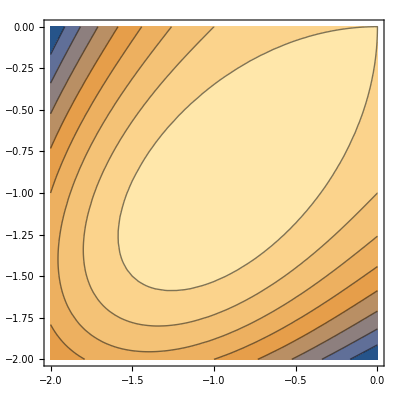

-Graphics3D-

-Graphics3D-

```mathematica
(*Построим линии уровня данной функции и локализуем точку экстремума*)
G=ContourPlot[f[x,y],{x,-2,0},{y,-2,0}]
(*Построим график данной функции в окрестности точки экстремума*)
G3D=Plot3D[f[x,y],{x,0,2},{y,1,3},PlotRange->All]
```

```mathematica
(*Зададим параметр, отражающий характер точки экстремума.
Если M=1, то точка экстремума - точка минимума.
Если M=-1, то точка экстремума - точка максимума*)
M=-1;
(*Зададим вспомогательную функцию*)
g[x_,y_]=M*f[x,y];
(*Найдем градиент данной функции и выполним его нормировку*)
Gradg=Grad[g[x,y],{x,y}];
n[x_,y_]=Gradg/Norm[Gradg];
(*Зададим точность вычислений*)
ϵ=10^(-3);
(*Зададим начальный шаг приближения*)
λ=1;
(*Зададим начальное приближение к точке экстремума*)
M0={-2,0};
(*Найдем первое приближение к точке экстремума*)
(*M1=M0-λ*N[n[M0[[1]],M0[[2]]]];*)
(*Зададим переменную для подсчета количества приближений*)
k=0;
It={M0};
(*Реализуем алгоритм градиентного поиска точки минимума*)
While[λ≥ϵ,
M1=M0-λ*N[n[M0[[1]],M0[[2]]]];
If[g[M0[[1]],M0[[2]]]≥g[M1[[1]],M1[[2]]],
M0=M1;
k=k+1;
It=AppendTo[It,M0],
λ=λ/2
]
]
Print["Точка экстремума имеет вид: ",M1]
Print["Количество приближений к точке экстремума равно: ",k]
```

Точка экстремума имеет вид: {-1.00083,-0.999133}

Количество приближений к точке экстремума равно: 6

```mathematica
(*Выполним анимацию приближений к точке экстремума*)
GIt=ListLinePlot[It,PlotStyle->Orange];
Animate[Show[G,GIt,ListPlot[{It[[i]]},PlotStyle->Red]],{i,1,k+1,1},AnimationRunning->False]
```